Coded by Manish J. Thapa for Advanced Kinteics class at ETH Zurich

## Section 1.

Ex. 1

```mathematica
F[x_]:= a x^2+b x+c
```

```mathematica
param={a->1/2,b->3,c->-1};(*such right arrows assign number to parameters. very useful!*)
```

```mathematica
F[x]//.param
```

-1+3 x+x^2/2

```mathematica
F[3]//.param
```

25/2

```mathematica
N[F[3]]//.param
```

12.5

```mathematica
F[1/3]//.param
```

1/18

```mathematica
N[%]
```

0.0555556

```mathematica
Sin[x]
```

Sin[x]

```mathematica
F[%]//.param
```

-1+3 Sin[x]+Sin[x]^2/2

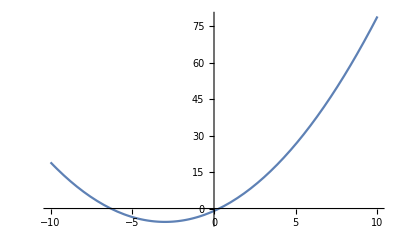

```mathematica
Plot[F[x]//.param,{x,-10,10},PlotRange->All](*sometimes mathematica does not output the plot in the full range. to avoid such issues set PlotRange to All*)
```

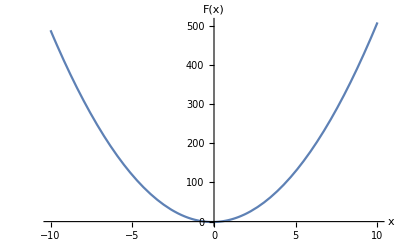

```mathematica
Plot[F[x]//.{a->5,b->1,c->-1},{x,-10,10},AxesLabel->{"x","F(x)"}]
```

```mathematica
(*Problem 1*)
parama = {a->-1, b->2, c->2};
paramb = {a->0,b->-4,c->-9};
```

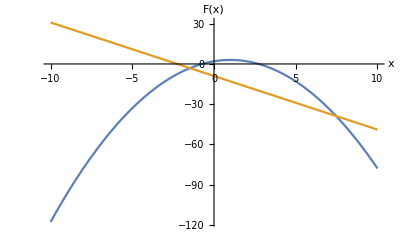

```mathematica
Plot[{F[x]//.parama,F[x]//.paramb},{x,-10,10},AxesLabel->{"x","F(x)"}]
```

```mathematica
K[x_,y_]:=Exp[-x^2] Exp[-y^2];
```

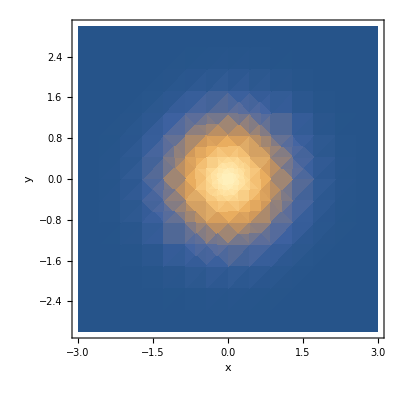

```mathematica
DensityPlot[K[x,y],{x,-3,3},{y,-3,3},PlotRange->All,FrameLabel->{x,y}](*frame label should be used for density plots like this to label the axes*)
```

```mathematica
Plot3D[K[x,y],{x,-3,3},{y,-3,3},PlotRange->All] (*AxesLabel option should be used for labelling 3D plots like this*)
```

-Graphics3D-

```mathematica
(*Problem 2*)
H[x_,y_,z_]:=2x^2+3y^3+6z;
```

```mathematica
Plot3D[H[x,y,z]//.{z->2},{x,-3,3},{y,-3,3},PlotRange->All,AxesLabel->{x,y,H}]
```

-Graphics3D-

```mathematica
Table[x^2,{x,1,10,1}](*one of the handy tools. can have more control over setting up points in the grid*)
```

```mathematica
(**Problem 3**)
```

```mathematica
tabKxy=Table[K[x,y],{x,-3,3,1},{y,-3,3,1}]
```

{{1/ⅇ^18,1/ⅇ^13,1/ⅇ^10,1/ⅇ^9,1/ⅇ^10,1/ⅇ^13,1/ⅇ^18},{1/ⅇ^13,1/ⅇ^8,1/ⅇ^5,1/ⅇ^4,1/ⅇ^5,1/ⅇ^8,1/ⅇ^13},{1/ⅇ^10,1/ⅇ^5,1/ⅇ^2,1/ⅇ,1/ⅇ^2,1/ⅇ^5,1/ⅇ^10},{1/ⅇ^9,1/ⅇ^4,1/ⅇ,1,1/ⅇ,1/ⅇ^4,1/ⅇ^9},{1/ⅇ^10,1/ⅇ^5,1/ⅇ^2,1/ⅇ,1/ⅇ^2,1/ⅇ^5,1/ⅇ^10},{1/ⅇ^13,1/ⅇ^8,1/ⅇ^5,1/ⅇ^4,1/ⅇ^5,1/ⅇ^8,1/ⅇ^13},{1/ⅇ^18,1/ⅇ^13,1/ⅇ^10,1/ⅇ^9,1/ⅇ^10,1/ⅇ^13,1/ⅇ^18}}

```mathematica
ListPlot3D[tabKxy,PlotRange->All]
```

-Graphics3D-

```mathematica
(**Problem 4**)
```

```mathematica
ListPlot3D[Table[K[x,y],{x,-3,3,0.1},{y,-3,3,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
(**One needs more fine-graining to make the plot smoother just as in previous exercise. To achieve this just reduce the step-size to something smaller**)
```

Ex. 2

```mathematica
G[α_,θ_]:=Sin[α]+Cos[θ]
```

```mathematica
D[G[α,θ],α]
```

Cos[α]

```mathematica
D[G[α,θ],θ]
```

-Sin[θ]

```mathematica
D[D[G[α,θ],α],α]
```

-Sin[α]

```mathematica
D[G[α,θ],{α,2}](*one can also specify an integer to perform derivative several times*)
```

-Sin[α]

```mathematica
Integrate[G[α,θ],α](*definite integral over just one variable*)
```

-Cos[α]+α Cos[θ]

```mathematica
Integrate[G[α,θ],α,θ](*indefinite integral over two variables*)
```

-θ Cos[α]+α Sin[θ]

```mathematica
Int=Integrate[G[α,θ],{α,α1,α2}]
```

Cos[α1]-Cos[α2]+(-α1+α2) Cos[θ]

```mathematica
param1={α1->π,α2->2π};
```

```mathematica
Int//.param1
```

-2+π Cos[θ]

```mathematica
(*Problem 1*)
```

```mathematica
func1=F[x]//.parama;
```

```mathematica
func2=F[x]//.paramb;
```

```mathematica
sol1=Solve[D[func1,x]==0,x](*Solve module can be used to solve system of equation(s)*)
```

{{x→1}}

```mathematica
D[func1,{x,2}](*confirms maximum*)
```

-2

```mathematica
sol2=Solve[D[func2,x]==0,x](*There are no values for D[F[x]]==0, so there are no stationary points. func2 is a straight line so this makes sense.*)
```

{}

```mathematica
Integrate[func1,{x,-10,10}](*integrating the function over a range*)
```

-1880/3

```mathematica
Integrate[func2,{x,-10,10}]
```

-180

Ex. 3

```mathematica
sol=DSolve[{x'[t]==a x[t]+b},x,t][[1]](*solve 1D ordinary differential equation*)
```

{x→Function[{t},-b/a+ⅇ^(a t) C[1]]}

```mathematica
ans=x[t]//.sol(*solution of the differential equation*)
```

-b/a+ⅇ^(a t) C[1]

```mathematica
(*Problem 1*)
```

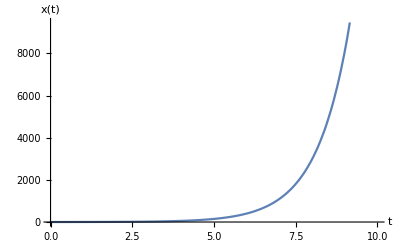

```mathematica
Plot[ans//.{C[1]->1,b->1,a->1},{t,0,10},AxesLabel->{"t","x(t)"}]
```

```mathematica
(*Problem 2*)
```

```mathematica
order2sol=DSolve[{x''[t]==a x[t]+b},x,t][[1]](*solve 1D ordinary differential equation*)
```

{x→Function[{t},-b/a+ⅇ^(√a t) C[1]+ⅇ^(-√a t) C[2]]}

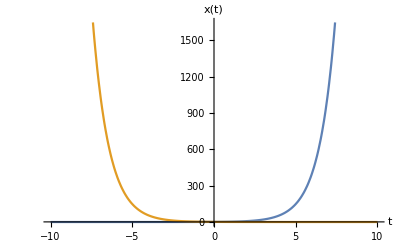

```mathematica
Plot[{x[t]//.order2sol//.{a->1,b->1,C[1]->1,C[2]->0},x[t]//.order2sol//.{a->1,b->1,C[1]->0,C[2]->1}},{t,-10,10},AxesLabel->{"t","x(t)"}]
```

Ex. 4

```mathematica
mat={{1,9},{2,-3}};
mat (*Mathematica's array representation of the matrix*)
```

{{1,9},{2,-3}}

```mathematica
mat//MatrixForm (*MatrixForm makes more sense in the context of matrices and vectors*)
```

(1 | 9
2 | -3)

```mathematica
Inverse[mat]
```

{{1/7,3/7},{2/21,-1/21}}

```mathematica
Det[mat]
```

-21

```mathematica
Transpose[mat]
```

{{1,2},{9,-3}}

```mathematica
mat1={{-1,2},{-3,4}};
```

```mathematica
mat.mat1
```

{{-28,38},{7,-8}}

```mathematica
mat1.mat (*Matrix multiplication order matters!*)
```

{{3,-15},{5,-39}}

```mathematica
mat*mat1
```

{{-1,18},{-6,-12}}

```mathematica
mat1*mat (*But in element-wise multiplication it doesn't!*)
```

{{-1,18},{-6,-12}}

```mathematica
Eigenvalues[mat]
```

{-1-√22,-1+√22}

```mathematica
Eigenvectors[mat](*beware eigenvectors may not be normalized. particularly important in quantum mechanics*)
```

{{1/2 (2-√22),1},{1/2 (2+√22),1}}

```mathematica
(*Problem 1*)
```

```mathematica
matA={{12,-4,0,2},{1,6,-21,0},{5,17,-3,9},{16,-11,0,1}};
```

```mathematica
matA//MatrixForm
```

(12 | -4 | 0 | 2
1 | 6 | -21 | 0
5 | 17 | -3 | 9
16 | -11 | 0 | 1)

```mathematica
Inverse[matA]//MatrixForm
```

(403/706 | 9/706 | -63/706 | -239/706
487/706 | 5/353 | -35/353 | -172/353
475/2118 | -91/2118 | -23/706 | -329/2118
-1091/706 | -17/353 | 119/353 | 373/353)

```mathematica
InvA=Inverse[matA];
```

```mathematica
matA.InvA //MatrixForm(*Inverse times the matrix should give us the identity matrix*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*Problem 2*)
```

```mathematica
eigval=Eigenvalues[mat]
```

{-1-√22,-1+√22}

```mathematica
eigvec=Eigenvectors[mat]
```

{{1/2 (2-√22),1},{1/2 (2+√22),1}}

```mathematica
v1=Normalize[eigvec[[1]]](*normalizing eigenvectors*)
```

{(2-√22)/(2 √(1+1/4 (-2+√22)^2)),1/(√(1+1/4 (-2+√22)^2))}

```mathematica
v2=Normalize[eigvec[[2]]]
```

{(2+√22)/(2 √(1+1/4 (2+√22)^2)),1/(√(1+1/4 (2+√22)^2))}

```mathematica
(*Problem 3*)
```

```mathematica
eigvec1=Eigenvectors[mat1]
```

{{2,3},{1,1}}

```mathematica
eigval1=Eigenvalues[mat1]
```

{2,1}

```mathematica
Solve[a*eigvec1[[1]]==mat1.eigvec1[[1]],a](*first eigenvalue*)
```

{{a→2}}

```mathematica
Solve[a*eigvec1[[2]]==mat1.eigvec1[[2]],a](*second eigenvalue*)
```

{{a→1}}

```mathematica
(*or*)
```

```mathematica
eigval1[[1]]*eigvec1[[1]]-mat1.eigvec1[[1]]
```

{0,0}

```mathematica
eigval1[[2]]*eigvec1[[2]]-mat1.eigvec1[[2]]
```

{0,0}

## Section 2

Ex. 5

```mathematica
(*Classical Mechanics*)
```

```mathematica
V[x_]:=1/2 m ω^2x^2; (*harmonic potential well*)
```

```mathematica
param2={m->5,ω->0.1};
```

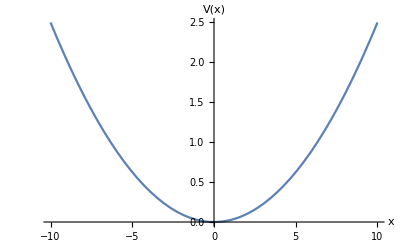

```mathematica
Plot[V[x]//.param2,{x,-10,10},AxesLabel->{"x","V(x)"}]
```

```mathematica
force=-D[V[x[t]],x[t]] (*newton's equation of motion*)
```

-m ω^2 x[t]

```mathematica
traj=DSolve[{m x''[t]==force},x,t][[1]](*solves newton's equation of motion for a classical path*)
```

{x→Function[{t},C[1] Cos[t ω]+C[2] Sin[t ω]]}

```mathematica
coeff=Solve[{a==x[t]//.traj//.{t->0},b==x[t]//.traj//.{t->τ}},{C[1],C[2]}][[1]](*computing the prefactors of x[t] using boundary conditions*)
```

{C[1]→a,C[2]→-a Cot[τ ω]+b Csc[τ ω]}

```mathematica
xt=x[t]//.traj//.coeff;
```

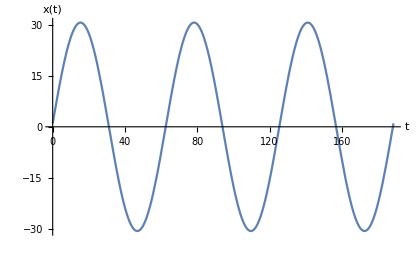

```mathematica
Plot[xt//.{a->1,b->10,τ->3}//.param2,{t,0,6π/0.1},AxesLabel->{"t","x(t)"}]
```

```mathematica
pt=m*D[xt,t](*computing momentum as a derivative of xt*)
```

m (ω Cos[t ω] (-a Cot[τ ω]+b Csc[τ ω])-a ω Sin[t ω])

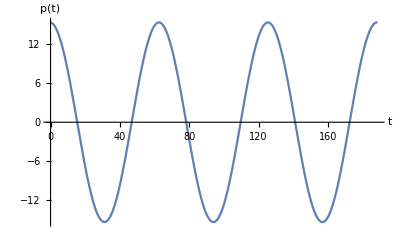

```mathematica
Plot[pt//.{a->1,b->10,τ->3}//.param2,{t,0,6π/0.1},AxesLabel->{"t","p(t)"}]
```

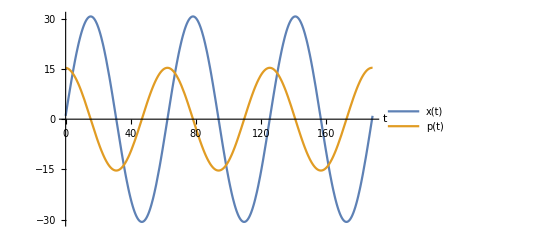

```mathematica
Plot[{xt//.{a->1,b->10,τ->3}//.param2,pt//.{a->1,b->10,τ->3}//.param2},{t,0,6π/0.1},AxesLabel->{"t",""},PlotLegends->{"x(t)","p(t)"}]
```

```mathematica
(*At the stationary points, the oscillator demonstrates maximum displacement and minimum momentum. This means at equilibrium, the oscillator has maximiim potential energy but minimum (or zero) kinetic energy*)
```

Ex. 6

```mathematica
(*Quantum Mechanics*)
```

```mathematica
Clear[h,m,ψ,ω](*clearing variables that have been used above. do not use the same variable without first clearing it*)
```

```mathematica
param3={m->1,ω->1};
```

```mathematica
schrodsol=DSolve[{-h^2/(2 m)ψ''[x]==(h ω/2 -1/2 m ω^2 x^2 )ψ[x]},ψ,x][[1]](*solving schrodinger equation for ground state wavefunction. energy is hω/2*)
```

{ψ→Function[{x},ⅇ^(-(m x^2 ω)/(2 h)) C[1]+(ⅇ^(-(m x^2 ω)/(2 h)) √h √π C[2] Erfi[(√m x √ω)/(√h)])/(2 √m √ω)]}

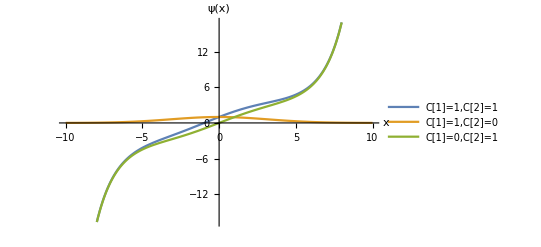

```mathematica
Plot[{ψ[x]//.schrodsol//.{ω->0.1,m->1,h->1,C[1]->1,C[2]->1},ψ[x]//.schrodsol//.{ω->0.1,m->1,h->1,C[1]->1,C[2]->0},ψ[x]//.schrodsol//.{ω->0.1,m->1,h->1,C[1]->0,C[2]->1}},{x,-10,10},AxesLabel->{"x","ψ(x)"},PlotLegends->{"C[1]=1,C[2]=1","C[1]=1,C[2]=0","C[1]=0,C[2]=1"}]
```

```mathematica
psi=ψ[x]//.schrodsol//.{C[2]->0}
```

ⅇ^(-(m x^2 ω)/(2 h)) C[1]

```mathematica
Integrate[Abs[psi]^2,{x,-Infinity,Infinity}] (*normalization*)
```

ConditionalExpression[(√π Abs[C[1]]^2)/(√Re[(m ω)/h]),Re[(m ω)/h]≥0]

```mathematica
norm=Assuming[Re[(m ω)/h]≥0,Integrate[Abs[psi]^2,{x,-Infinity,Infinity}]] (*can use assumption in this manner to avoid ugly conditional expressions*)
```

(√π Abs[C[1]]^2)/(√Re[(m ω)/h])

```mathematica
coeff=Solve[norm==1,C[1]][[2]](*solving for normalization constant C[1]*)
```

{C[1]→Re[(m ω)/h]^(1/4)/π^(1/4)}

```mathematica
ψ=psi//.coeff(*final normalized wavefunction for ground state*)
```

(ⅇ^(-(m x^2 ω)/(2 h)) Re[(m ω)/h]^(1/4))/π^(1/4)

```mathematica
d2ψdx2=D[D[ψ,x],x]
```

-(ⅇ^(-(m x^2 ω)/(2 h)) m ω Re[(m ω)/h]^(1/4))/(h π^(1/4))+(ⅇ^(-(m x^2 ω)/(2 h)) m^2 x^2 ω^2 Re[(m ω)/h]^(1/4))/(h^2 π^(1/4))

```mathematica
-h^2/(2 m) d2ψdx2+1/2 m ω^2 x^2 ψ-h ω/2 ψ//FullSimplify (*plugging the wavefunction into time-independent schrodinger equation, to see if it is the solution indeed*)
```

0

```mathematica
(*Question: What does the time dependent wavefunction for this ground state look like?*)
```

```mathematica
(*Answer: ψ will have another component multiplied to it. This component comes from solving time-dependent part and is is e^(-I ω/2 t)*)
```

```mathematica
$Assumptions={h>0}(*one can also set assumptions like this in the beginning of the code*)
```

{h>0}

```mathematica
(**Uncertainty in x**)
```

```mathematica
meanx=Integrate[Conjugate[ψ](x ψ)//.param3,{x,-Infinity,Infinity}]
```

0

```mathematica
meanx=Integrate[Conjugate[ψ](x ψ)//.param3,{x,-Infinity,Infinity},Assumptions->h>0]
```

0

```mathematica
sdx=Integrate[Conjugate[ψ](x^2 ψ)//.param3,{x,-Infinity,Infinity}]//FullSimplify
```

h/2

```mathematica
errx=√(sdx-meanx^2)
```

(√h)/(√2)

```mathematica
(**Uncertainty in p**)
```

```mathematica
meanp=Integrate[Conjugate[ψ](-I h D[ψ,x])//.param3,{x,-Infinity,Infinity}]
```

0

```mathematica
sdp=Integrate[Conjugate[ψ](-h^2 D[D[ψ,x],x])//.param3,{x,-Infinity,Infinity}]//FullSimplify
```

h/2

```mathematica
errp=√(sdp-meanp^2)
```

(√h)/(√2)

```mathematica
f=errx*errp
```

h/2

```mathematica
(*Question: What is f called in quantum mechanics? What does your final answer to f tell you about this ground state wavefunction?*)
```

```mathematica
(*Answer: f is the Heisenberg's uncertainty relation. f is always greater than or equal to 1/2 h, where h is planck's constant. 
For the ground state wavefunction we have, f is exactly equal to 1/2 h suggesting the system behaves classically*)
```

```mathematica
(***********************************THE END*********************************)
```